## Calculate the tangent points from (0,0) to an ellipse (a,b) at (X0,Y0)

Tangents (x-X0)^2/a^2+ (y-Y0)^2/b^2==1 should have a slope dy/dx=m .

```mathematica
(D[(x-X0)^2/a^2,x]+D[(y-Y0)^2/b^2,y]m)/2//Expand//Simplify
```

(x-X0)/a^2+(m (y-Y0))/b^2

```mathematica
sol$={x,y}/.Solve[
{
(x-X0)/a^2+(m (y-Y0))/b^2==0, (* m is the slope of the tangent *)
m==y/x,  (* Line through (0,0) with the slope m *)
(x-X0)^2/a^2+ (y-Y0)^2/b^2==1  (* Ellipse *)
},
{x,y,m}
]//FullSimplify[#,Assumptions->{a>0&&b>0&&X0>0&&Y0>0}]&
```

{{(b^2 X0^3+a^2 (-b^2 X0+Y0 (X0 Y0+√(b^2 X0^2+a^2 (-b^2+Y0^2)))))/(b^2 X0^2+a^2 Y0^2),(a^2 (-b^2 Y0+Y0^3)+b^2 X0 (X0 Y0-√(b^2 X0^2+a^2 (-b^2+Y0^2))))/(b^2 X0^2+a^2 Y0^2)},{(b^2 X0^3-a^2 (b^2 X0+Y0 (-X0 Y0+√(b^2 X0^2+a^2 (-b^2+Y0^2)))))/(b^2 X0^2+a^2 Y0^2),(a^2 (-b^2 Y0+Y0^3)+b^2 X0 (X0 Y0+√(b^2 X0^2+a^2 (-b^2+Y0^2))))/(b^2 X0^2+a^2 Y0^2)}}

## Test plot

{{0.492031,1.937},{-1.43049,1.81684}}

{{0.992031,-0.0629981},{-0.930492,-0.183156}}

{356.366,191.136}

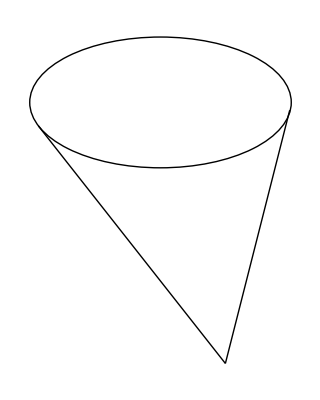

```mathematica
Block[
{a=1,b=0.5,X0=-0.5,Y0=2},
Print[sol$];
Print[#-{X0,Y0}&/@sol$];
Print[360+180/π*ArcTan[#⟦1⟧,#⟦2⟧]&/@(#-{X0,Y0}&/@sol$)];
Graphics[{
Circle[{X0,Y0},{a,b}],
Line[{{0,0},sol$⟦1⟧}],
Line[{{0,0},sol$⟦2⟧}]
}
]
]
```

## Generate TEX code for TikZ

```mathematica
texConvert[e_]:=StringReplace[ToString@InputForm@e,{
"X0"->"(#1)","Y0"->"(#2)",
"a"->"#3","b"->"#4",
"Sqrt"->"sqrt",
"["->"(","]"->")",
"PP"->"(\\NC@PP)","QQ"->"(\\NC@QQ)","RR"->"(\\NC@RR)"
}]
```

```mathematica
sol2$=sol$/.{
√(b^2 X0^2+a^2 (-b^2+Y0^2))->PP,
b^2 X0^2+a^2 Y0^2->QQ
}//Simplify[#,Assumptions->{b^2 X0^2+a^2  (-b^2+Y0^2)==RR}]&
```

{{(RR X0+a^2 PP Y0)/QQ,(-b^2 PP X0+RR Y0)/QQ},{(RR X0-a^2 PP Y0)/QQ,(b^2 PP X0+RR Y0)/QQ}}

```mathematica
texConvert/@Flatten@sol2$;
"\\newcommand{\\ncCoords}[4]{\n"<>
"  \\def\\NCellipse{(#1,#2) circle (#3 and #4)}\n"<>
"  \\def\\NC@PP{ "<>texConvert[√(b^2 X0^2+a^2 (-b^2+Y0^2))]<>" }\n"<>
"  \\def\\NC@QQ{ ( "<>texConvert[b^2 X0^2+a^2 Y0^2]<>" ) }\n"<>
"  \\def\\NC@RR{ ( "<>texConvert[b^2 X0^2+a^2(-b^2+Y0^2)]<>" ) }\n"<>
"  \\def\\Xa{ "<>%⟦1⟧<>" }\n"<>
"  \\def\\Xb{ "<>%⟦3⟧<>" }\n"<>
"  \\def\\Ya{ "<>%⟦2⟧<>" }\n"<>
"  \\def\\Yb{ "<>%⟦4⟧<>" }\n"<>
"  \\def\\NCwedge{({\\Xa},{\\Ya}) -- (0,0) -- ({\\Xb},{\\Yb})}\n"<>
"  \\def\\NCwedgeClip{({0.99*\\Xa},{0.97*\\Ya}) -- (0,0) -- ({0.99*\\Xb},{0.97*\\Yb})}\n"<>
"}"
```

\newcommand{\ncCoords}[4]{
  \def\NCellipse{(#1,#2) circle (#3 and #4)}
  \def\NC@PP{ sqrt(#4^2*(#1)^2 + #3^2*(-#4^2 + (#2)^2)) }
  \def\NC@QQ{ ( #4^2*(#1)^2 + #3^2*(#2)^2 ) }
  \def\NC@RR{ ( #4^2*(#1)^2 + #3^2*(-#4^2 + (#2)^2) ) }
  \def\Xa{ ((\NC@RR)*(#1) + #3^2*(\NC@PP)*(#2))/(\NC@QQ) }
  \def\Xb{ ((\NC@RR)*(#1) - #3^2*(\NC@PP)*(#2))/(\NC@QQ) }
  \def\Ya{ (-(#4^2*(\NC@PP)*(#1)) + (\NC@RR)*(#2))/(\NC@QQ) }
  \def\Yb{ (#4^2*(\NC@PP)*(#1) + (\NC@RR)*(#2))/(\NC@QQ) }
  \def\NCwedge{({\Xa},{\Ya}) -- (0,0) -- ({\Xb},{\Yb})}
  \def\NCwedgeClip{({0.99*\Xa},{0.97*\Ya}) -- (0,0) -- ({0.99*\Xb},{0.97*\Yb})}
}